```mathematica
SetOptions[EvaluationNotebook[],LightDark->"Light"];
SetDirectory[NotebookDirectory[]];
```

## Renormalisation

```mathematica
(* copied from Geometrical Phyllotaxis *)
euclideanWindingNumberPair[mn_] := Module[{m,n,u,v},
{{m,u},{n,v}}= euclideanMatrixProduct[mn];
{u,v}
];

eMatrix = ({
 {1, 1},
 {0, 1}
});
sMatrix=({
 {0, 1},
 {1, 0}
});

euclideanMatrixProduct[mn_] := Module[{q,res},
q = euclideanQCoefficients[mn];
res= (Map[  MatrixPower[eMatrix,#] . sMatrix &,q]);
res= If[Length[res]>0,Dot@@res,IdentityMatrix[2]];
res = sMatrix . res;

res
]/; NumericQ[First[mn]];
euclideanMatrixProduct[{1,0}] = ({
 {0, -1},
 {1, 0}
});
euclideanMatrixProduct[{0,1}] = ({
 {1, 0},
 {0, -1}
});
euclideanDelta[mn_]  := Det@euclideanMatrixProduct[mn];


euclideanQCoefficients[{m_,n_}] := Module[{r,q,i},
	i=0;
	r[-1]=n; 
	r[0] = m;
	While[r[i] > 0  , 
		q[i] = Floor[r[i-1]/r[i]];
		r[i+1] = r[i-1] - q[i]*r[i];
		i++;
	];
 Table[q[j],{j,0,i-1}]
];
```

```mathematica
z1OfMNTheta[{m_,n_},θ_]:= Module[{delta,u,v,gFunction,z1},
delta=euclideanDelta[{m,n}];
{u,v}=euclideanWindingNumberPair[{m,n}];
If[m v - n u != delta,Print["cLC ", delta, {m,n},{u,v}]];
gFunction[w_] := (u w - v)/( m w -n);
z1=gFunction[Exp[ I θ]];
delta * z1
];

pmnOfMNTheta[{m_,n_},θ_]:= Module[{z1,u,v,zm,zn},
z1= z1OfMNTheta[{m,n},θ];
{u,v}=euclideanWindingNumberPair[{m,n}];

zm = m z1 - u;
 zn = n z1 - v;
toCartesian [zm+zn]
];
pmOfMNTheta[{m_,n_},θ_]:= Module[{z1,u,v,zm,zn},
z1=z1OfMNTheta[{m,n},θ];
{u,v}=euclideanWindingNumberPair[{m,n}];

zm = m z1 - u;
toCartesian [zm]
];
pnOfMNTheta[{m_,n_},θ_]:= Module[{z1,u,v,zm,zn},
z1= z1OfMNTheta[{m,n},θ];
{u,v}=euclideanWindingNumberPair[{m,n}];

 zn = n z1 - v;
toCartesian [zn]
];

toCartesian[z_] :=Module[{x,y},
{x,y}= Simplify[ComplexExpand[ReIm[z]]];
{x,y}
];
```

```mathematica
Clear[u,v,m,n];gFunction[w_] := (u w - v)(m Conjugate[w] -n)/(Abs[m w - n])^2;
```

```mathematica
{x,y}=Simplify[toCartesian[ Δ gFunction[d0 +  I h0]]/. vis/. Δ^2->1]  /. d0^2 m^2+h0^2 m^2-2 d0 m n+n^2-> denom
```

```mathematica
Simplify[Simplify[Expand[Simplify[denom (x^2+ y^2) /. Δ^2->1]]/. Δ^2->1] /. Δ-> m v - n u]
```

1/(denom m^2)(d0^2 m^2+h0^2 m^2-2 d0 m n+n^2) (1+d0^2 m^2 u^2+h0^2 m^2 u^2-n^2 u^2-2 d0 m^2 u v+2 m n u v)

```mathematica
denom*(x /. Δ-> m v - n u )
```

(-n u+m v) (d0^2 m u+h0^2 m u+n v-d0 (n u+m v))

```mathematica
norm= (u w - v)/(m w - n);
norm2= norm. Conjugate[norm]
```

(-v+u w)/(-n+m w).(-Conjugate[v]+Conjugate[u w])/(-Conjugate[n]+Conjugate[m w])

```mathematica
ComplexExpand[norm2/. w->Exp[I θ]]
```

(ⅇ^(ⅈ θ) u-v)/(ⅇ^(ⅈ θ) m-n).(ⅇ^(-ⅈ Conjugate[θ]) Conjugate[u]-Conjugate[v])/(ⅇ^(-ⅈ Conjugate[θ]) Conjugate[m]-Conjugate[n])

{(d0^2 m u+h0^2 m u+n v-d0 (n u+m v))/(d0^2 m^2+h0^2 m^2-2 d0 m n+n^2),(h0 (-n u+m v))/(d0^2 m^2+h0^2 m^2-2 d0 m n+n^2)}

```mathematica
vis=Solve[Δ== m v - n u , v][[1]];
{x1,y1}= (toCartesian[ Δ gFunction[Subscript[w, 0] Exp [I θ]]]/. vis /. Δ^2->1)
```

```mathematica
{xs,ys} =Simplify[Expand[{x1,y1}/. θ->π/2]/. {Δ^2->1,Subscript[w, 0]->s}]
```

{(n+n^2 u Δ+m^2 s^2 u Δ)/(m n^2+m^3 s^2),s/(n^2+m^2 s^2)}

```mathematica
Solve[s/(n2+m^2 s^2)==ysn,n2][[1]]
```

```mathematica
Simplify[xs/. {n^2->n2}/. Solve[s/(n2+m^2 s^2)==ysn,n2][[1]]]
```

(n ysn+s u Δ)/(m s)

```mathematica
{x1,y1} /. n^2-2 m n Cos[θ] Subscript[w, 0]+m^2 Subscript[w, 0]^2-> denom
```

{((n (n u+Δ))/m-(2 n u+Δ) Cos[θ] w_0+m u w_0^2)/denom,(Δ Sin[θ] w_0)/denom}

```mathematica
euclideanWindingNumberPair[{2,3}]
```

{1,1}

```mathematica
z1OfMNTheta[{2,3},π/2]
```

-5/13+ⅈ/13

```mathematica
pmOfMNTheta[{2,3},π/2]
```

{3/13,2/13}

```mathematica
mnPairs=Flatten[Table[Table[{j,i},{i,j+1,7}],{j,1,7}],1];
mnPairs=Select[mnPairs,GCD@@#==1&]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{2,3},{2,5},{2,7},{3,4},{3,5},{3,7},{4,5},{4,7},{5,6},{5,7},{6,7}}

```mathematica
GCD[{2,3}]
```

{2,3}

```mathematica
mnPairs={{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,5},{2,7},{3,4},{3,5},{4,5},{4,7},{5,6},{5,7},{6,7}}
pmnPairs = Map[pmnOfMNTheta[#,θ]&,mnPairs];
pmnPairs3D=MapIndexed[{First[#2],Splice[#1]}&,pmnPairs];
ParametricPlot3D[pmnPairs3D,{θ,1.01 * π/3,2 π/3},PlotRange->{Automatic,{0.5,0.7},{0,0.5}},PlotLegends->Map[ToString,mnPairs],AxesOrigin->{0,1/2,0}]
```

{{1,2},{1,3},{1,4},{1,5},{1,6},{2,3},{2,5},{2,7},{3,4},{3,5},{4,5},{4,7},{5,6},{5,7},{6,7}}

-Graphics3D-

```mathematica
ParametricPlot[pmnPairs,{θ,1.01 * π/3,2 π/3},PlotRange->All,PlotLegends->None]
```

```mathematica
angleForOrthogonalLatticeChain[{m_,n_},circumference_]:= Module[{z1,angle},
z1=z1OfMNTheta[{m,n},π/2];
angle=Arg[z1];
angle
];
```

## Chains

```mathematica
addByAngle[centres_,angle_] :=Append[centres,Last[centres]+2*(N@{Cos[angle],Sin[angle]})];
```

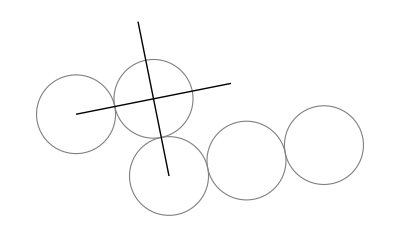

```mathematica
angle=N@Abs[angleForOrthogonalLatticeChain[{2,3},4]];
pm=2*{Cos[angle],Sin[angle]};
pn = 2*{Cos[angle+π/2],Sin[angle+π/2]};
angles={angle,angle-π/2,angle,angle};
centres=Fold[addByAngle,{{-4,0}},angles];
ffs=Directive[FaceForm[None],EdgeForm[Gray]];
Graphics[{ffs,Disk[#,1]&/@centres,
Line[{{centres[[1]], centres[[1]]+2 pm},{centres[[2]]-pn, centres[[2]]+ pn}}]}]
```

```mathematica
centres
```

{{-4,0},{-2.03884,0.392232},{-1.64661,-1.56893},{-2.03884,0.392232}}